```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
v="9";
p="0.1";

g5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];
g10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];
g20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l20k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l20k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l20k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];
g30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];
g40k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l40k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v40k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l40k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av40k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l40k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];
g50k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l50k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v50k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l50k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av50k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l50k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];
```

```mathematica
ngap="4";
nvel="4";
jj=StringToStream[ngap];
ng= Read[jj,Number];
ii=StringToStream[nvel];
nv= Read[ii,Number];
ClearAll[d0,z,α];
d0=0.0674;
z=0.65;
α=0.65;
gap5v9=Table[{g5k1[[All,1]][[j]],Sum[g5k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g5k1]}];
vel5v9=Table[{v5k1[[All,1]][[j]],Sum[v5k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v5k1]}];
avel5v9=Table[{av5k1[[All,1]][[j]],av5k1[[All,2]][[j]]},{j,1,Length[av5k1]}];
gap10v9=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g10k1]}];
vel10v9=Table[{v10k1[[All,1]][[j]],Sum[v10k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v10k1]}];
avel10v9=Table[{av10k1[[All,1]][[j]],av10k1[[All,2]][[j]]},{j,1,Length[av10k1]}];
gap20v9=Table[{g20k1[[All,1]][[j]],Sum[g20k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g20k1]}];
vel20v9=Table[{v20k1[[All,1]][[j]],Sum[v20k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v20k1]}];
avel20v9=Table[{av20k1[[All,1]][[j]],av20k1[[All,2]][[j]]},{j,1,Length[av20k1]}];
gap30v9=Table[{g30k1[[All,1]][[j]],Sum[g30k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g30k1]}];
vel30v9=Table[{v30k1[[All,1]][[j]],Sum[v30k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v30k1]}];
avel30v9=Table[{av30k1[[All,1]][[j]],av30k1[[All,2]][[j]]},{j,1,Length[av30k1]}];
gap40v9=Table[{g40k1[[All,1]][[j]],Sum[g40k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g40k1]}];
vel40v9=Table[{v40k1[[All,1]][[j]],Sum[v40k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v40k1]}];
avel40v9=Table[{av40k1[[All,1]][[j]],av40k1[[All,2]][[j]]},{j,1,Length[av40k1]}];
gap50v9=Table[{g50k1[[All,1]][[j]],Sum[g50k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g50k1]}];
vel50v9=Table[{v50k1[[All,1]][[j]],Sum[v50k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v50k1]}];
avel50v9=Table[{av50k1[[All,1]][[j]],av50k1[[All,2]][[j]]},{j,1,Length[av50k1]}];
```

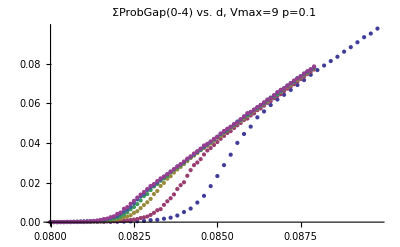

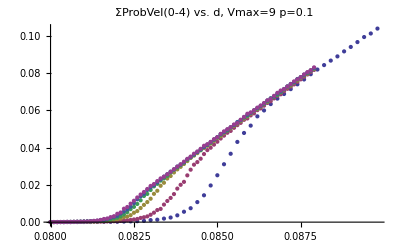

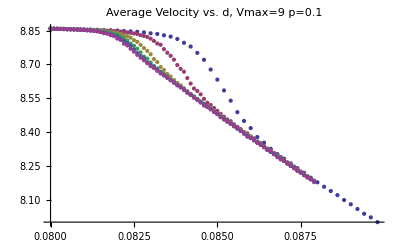

```mathematica
ListPlot[{gap5v9,gap10v9,gap20v9,gap30v9,gap40v9,gap50v9},PlotLabel->"ΣProbGap(0-"<>ngap<>") vs. d, Vmax="<>v<>"  p="<>p,PlotLegend->{"5k","10k","20k","30k","40k","50k"},LegendPosition->{1.1,-0.4},LegendShadow->None]
ListPlot[{vel5v9,vel10v9,vel20v9,vel30v9,vel40v9,vel50v9},PlotLabel->"ΣProbVel(0-"<>nvel<>") vs. d, Vmax="<>v<>"  p="<>p,PlotLegend->{"5k","10k","20k","30k","40k","50k"},LegendPosition->{1.1,-0.4},LegendShadow->None]
ListPlot[{avel5v9,avel10v9,avel20v9,avel30v9,avel40v9,avel50v9},PlotLabel->"Average Velocity vs. d, Vmax="<>v<>"  p="<>p,PlotRange->Full,PlotLegend->{"5k","10k","20k","30k","40k","50k"},LegendPosition->{1.1,-0.4},LegendShadow->None]
```

```mathematica
g[5]=gap5v9;
g[10]=gap10v9;
g[20]=gap20v9;
g[30]=gap30v9;
g[40]=gap40v9;
g[50]=gap50v9;
```

```mathematica
Do[
dgdd[l]=Table[{g[l][[All,1]][[i]],(-g[l][[All,2]][[i+2]]+8*g[l][[All,2]][[i+1]]-8*g[l][[All,2]][[i-1]]+g[l][[All,2]][[i-2]])/(12*(g[l][[All,1]][[i+1]]-g[l][[All,1]][[i-1]]))},{i,2,Length[g[l]]-2}];
,{l,{5,10,20,30,40,50}}]
```

```mathematica
Do[
i[l]=Interpolation[g[l]];
,{l,{5,10,20,30,40,50}}]
```

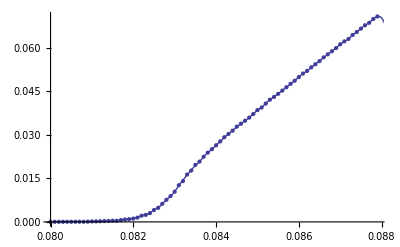

```mathematica
Show[{ListPlot[g[20]],Plot[i[20][x],{x,0.081,0.089}]}]
```

```mathematica
Plot[i[5][x],{x,0.081,0.089}]
```

-Graphics-

```mathematica
ND[{i[5][x]},x,0.084]
```

{1875.7}

```mathematica
Do[
δ=g[l][[All,1]][[12]]-g[l][[All,1]][[7]];
ndgdd[l]=Table[{g[l][[All,1]][[j]],(-i[l][g[l][[All,1]][[j]]+2*δ]+8*i[l][g[l][[All,1]][[j]]+δ]-8*i[l][g[l][[All,1]][[j]]-δ]+i[l][g[l][[All,1]][[j]]-2*δ])/(12*δ)},{j,2,Length[g[l]]-10}];
,{l,{5,10,20,30,40,50}}]
```

```mathematica
δ
```

0.0006

```mathematica
l=5;
j=Length[g[l]]-2
g[l][[All,1]][[j]]+2*δ
i[l][g[l][[All,1]][[j]]+2*δ]
j=2
g[l][[All,1]][[j]]+2*δ
i[l][g[l][[All,1]][[j]]+2*δ]
```

48

0.0896

0.0857995

2

0.0804

0.0000128856

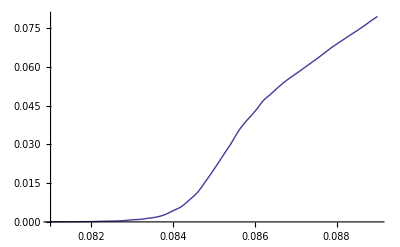

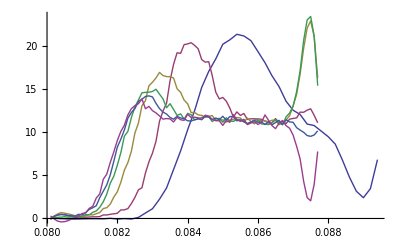

```mathematica
Plot[i[5][x],{x,0.081,0.089}]
ListLinePlot[{ndgdd[5],ndgdd[10],ndgdd[20],ndgdd[30],ndgdd[40],ndgdd[50]}]
```

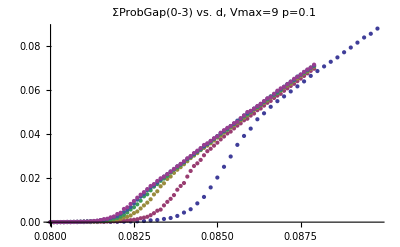

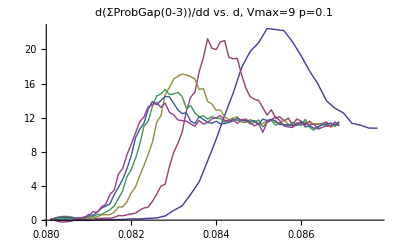

```mathematica
ListPlot[{g[5],g[10],g[20],g[30],g[40],g[50]},PlotLabel->"ΣProbGap(0-"<>ngap<>") vs. d, Vmax="<>v<>"  p="<>p,PlotLegend->{"5k","10k","20k","30k","40k","50k"},LegendPosition->{1.1,-0.4},LegendShadow->None]
ListLinePlot[{ndgdd[5],ndgdd[10],ndgdd[20],ndgdd[30],ndgdd[40],ndgdd[50]},PlotLabel->"d(ΣProbGap(0-"<>ngap<>"))/dd vs. d, Vmax="<>v<>"  p="<>p,PlotLegend->{"5k","10k","20k","30k","40k","50k"},LegendPosition->{1.1,-0.4},LegendShadow->None]
```

```mathematica
Do[
i[l]=Interpolation[g[l]];
id[l]=Interpolation[ndgdd[l]];
,{l,{5,10,20,30,40,50}}]
```

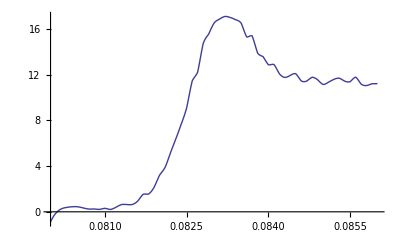

```mathematica
Plot[id[20][x],{x,0.08,0.086}]
```

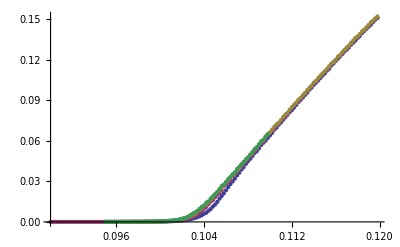

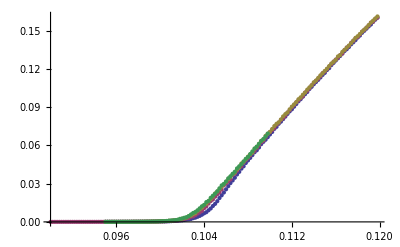

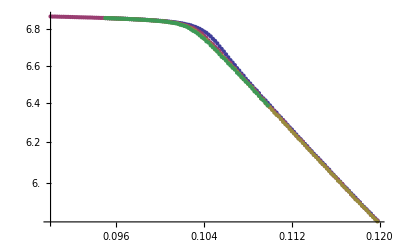

```mathematica
ListPlot[{gap5v7,gap10v7,gap20v7,gap30v7},PlotRange->Full]
ListPlot[{vel5v7,vel10v7,vel20v7,vel30v7}]
ListLogPlot[{avel5v7,avel10v7,avel20v7,avel30v7}]
```

```mathematica
ClearAll[ivel]
v=7;
```

```mathematica
ivel[v][5]=Interpolation[avel5v7];
ivel[v][10]=Interpolation[avel10v7];
ivel[v][20]=Interpolation[avel20v7];
ivel[v][30]=Interpolation[avel30v7];
```

```mathematica
δ=0.0008;
Do[
dvdd[l]=Table[{x,(ivel[l][x+δ]-ivel[l][x-δ])/(2*δ)},{x,0.098,0.11,0.0002}];
,{l,{5,10,20,30}}]
```

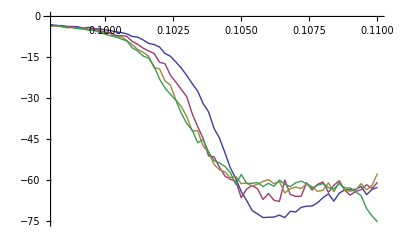

```mathematica
ListLinePlot[{dvdd[5],dvdd[10],dvdd[20],dvdd[30]}]
```

```mathematica
v=9;
ivel[v][5]=Interpolation[avel5v9];
ivel[v][10]=Interpolation[avel10v9];
ivel[v][20]=Interpolation[avel20v9];
ivel[v][30]=Interpolation[avel30v9];
ivel[v][40]=Interpolation[avel40v9];
ivel[v][50]=Interpolation[avel50v9];
```

```mathematica
v=9;
vel[v][5]= avel5v9;
vel[v][10]= avel10v9;
vel[v][20]= avel20v9;
vel[v][30]= avel30v9;
vel[v][40]= avel40v9;
vel[v][50]= avel50v9;
```

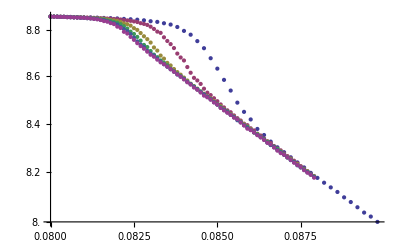

```mathematica
ListLogPlot[{avel5v9,avel10v9,avel20v9,avel30v9,avel40v9,avel50v9}]
```

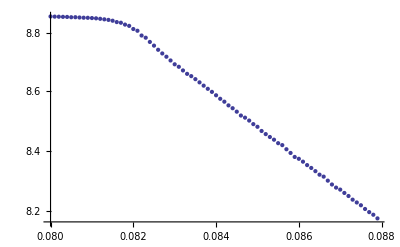

```mathematica
ListLogPlot[{avel50v9}]
```

```mathematica
ClearAll[dvdd]
```

```mathematica
δ=0.0008;
v=9;
Do[
dvdd[v][l]=Table[{x,(ivel[v][l][x+δ]-ivel[v][l][x-δ])/(2*δ)},{x,0.0815,0.087,0.0002}];
,{l,{5,10,20,30,40,50}}]
```

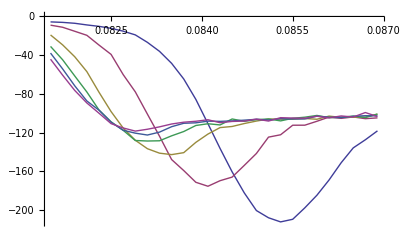

```mathematica
ListLinePlot[{dvdd[v][5],dvdd[v][10],dvdd[v][20],dvdd[v][30],dvdd[v][40],dvdd[v][50]}]
```

{{5000,212.336},{10000,175.487},{20000,142.794},{30000,128.737},{40000,122.55},{50000,118.487}}

{{Log[5000],5.35817},{Log[10000],5.16757},{Log[20000],4.9614},{Log[30000],4.85778},{Log[40000],4.80852},{Log[50000],4.77481}}

{{5000,0.0853},{10000,0.0841},{20000,0.0835},{30000,0.0831},{40000,0.0831},{50000,0.0829}}

{{5000,{}⟦1⟧},{10000,8.63966},{20000,8.65756},{30000,8.69307},{40000,8.68916},{50000,8.70567}}

{{5000,8.56219},{10000,8.63966},{20000,8.65756},{30000,8.69307},{40000,8.68916},{50000,8.70567}}

{{Log[5000],2.14736},{Log[10000],2.15636},{Log[20000],2.15843},{Log[30000],2.16253},{Log[40000],2.16208},{Log[50000],2.16397}}

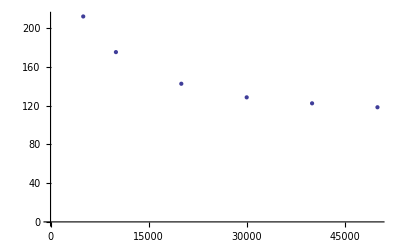

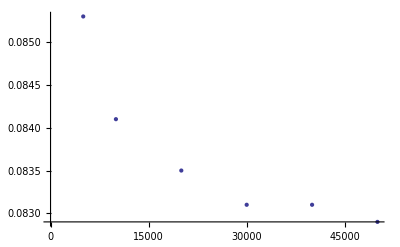

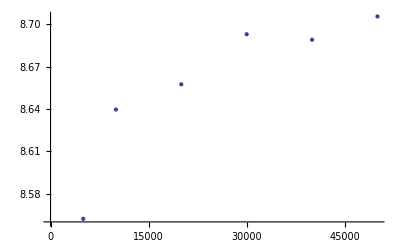

a0-b0 x

0.0812201+c0 x^-ex

{7.55969-0.259953 x, | Estimate | Standard Error | t-Statistic | P-Value
a0 | 7.55969 | 0.112584 | 67.1469 | 2.94716×10^-7
b0 | 0.259953 | 0.011343 | 22.9175 | 0.000021478}

{2.09213+0.00670486 x, | Estimate | Standard Error | t-Statistic | P-Value
a0 | 2.09213 | 0.00908703 | 230.232 | 2.13517×10^-9
b0 | -0.00670486 | 0.000915532 | -7.32346 | 0.00184988}

{0.0812201+0.114731/x^0.394429, | Estimate | Standard Error | t-Statistic | P-Value
ex | 0.394429 | 0.0238838 | 16.5145 | 0.0000787311
c0 | 0.114731 | 0.0257036 | 4.46362 | 0.0111292}

```mathematica
maxdvdd[v]=Table[{l*1000,Max[-dvdd[v][l][[All,2]]]},{l,{5,10,20,30,40,50}}]
Logmaxdvdd[v]=Table[{Log[maxdvdd[v][[All,1]][[i]]],Log[maxdvdd[v][[All,2]][[i]]]},{i,1,Length[maxdvdd[v]]}]

pmaxdvdd[v]=Table[{maxdvdd[v][[All,1]][[i]],Select[dvdd[v][maxdvdd[v][[All,1]][[i]]/1000],#[[2]]==-maxdvdd[v][[All,2]][[i]]&][[All,1]][[1]]},{i,1,Length[maxdvdd[v]]}]


vvpmaxdvdd[v]=Table[{pmaxdvdd[v][[All,1]][[i]],Select[vel[v][pmaxdvdd[v][[All,1]][[i]]/1000],#[[1]]==pmaxdvdd[v][[All,2]][[i]]&][[All,2]][[1]]},{i,1,Length[pmaxdvdd[v]]}]
vvpmaxdvdd[v]={{5000,8.562186875},{10000,8.63966},{20000,8.65756},{30000,8.69307},{40000,8.68916},{50000,8.70567}}

Logvvpmaxdvdd[v]=Table[{Log[vvpmaxdvdd[v][[All,1]][[i]]],Log[vvpmaxdvdd[v][[All,2]][[i]]]},{i,1,Length[vvpmaxdvdd[v]]}]


ListPlot[maxdvdd[v]]
ListPlot[pmaxdvdd[v]]
ListPlot[vvpmaxdvdd[v]]

ClearAll[a0,b0,d0,ex,c0]
model=a0-x*b0
model2=0.08122007942715888+c0*x^(-ex)

nlf1=NonlinearModelFit[Logmaxdvdd[v],model,{a0,b0},x];

nlf1[{"BestFit","ParameterTable"}]


nlf3=NonlinearModelFit[Logvvpmaxdvdd[v],model,{a0,b0},x];

nlf3[{"BestFit","ParameterTable"}]

nlf2=NonlinearModelFit[pmaxdvdd[v],model2,{ex,c0},x];

nlf2[{"BestFit","ParameterTable"}]
```

```mathematica
ivel[9][5][0.0853]
```

8.56219

```mathematica
a[v]=-0.00670485586502097
d0[v]=0.08122007942715888;
b0[v]=0.11473117226496223;
ex[v]=-0.39442912810725833;
```

-0.00670486

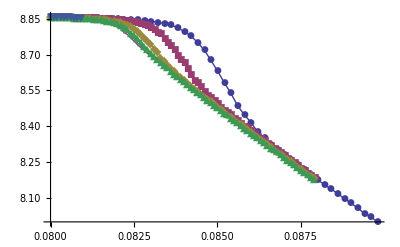

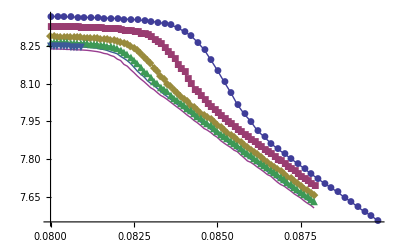

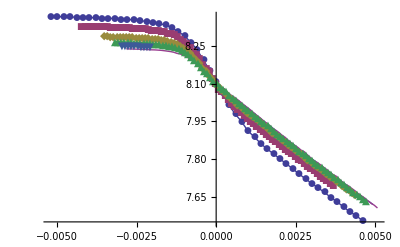

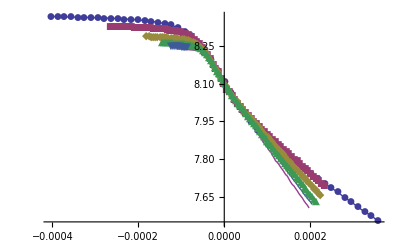

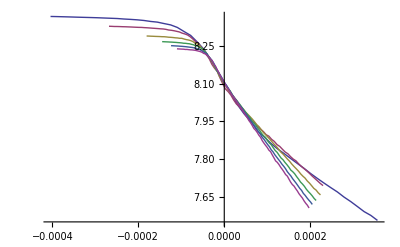

```mathematica
ClearAll[z]
z[v]=-0.3;
Do[
vels1[v][l]=Table[{vel[v][l][[All,1]][[i]],vel[v][l][[All,2]][[i]]*(1000*l)^a[v]},{i,1,Length[vel[v][l]]}];

vels2[v][l]=Table[{vel[v][l][[All,1]][[i]]-(d0[v]+b0[v]*(l*1000)^(ex[v])),vel[v][l][[All,2]][[i]]*(1000*l)^a[v]},{i,1,Length[vel[v][l]]}];

vels[v][l]=Table[{(vel[v][l][[All,1]][[i]]-(d0[v]+b0[v]*(l*1000)^(ex[v])))*(1000*l)^z[v],vel[v][l][[All,2]][[i]]*(1000*l)^a[v]},{i,1,Length[vel[v][l]]}];
,{l,{5,10,20,30,40,50}}]
pic0=ListPlot[{vel[v][5],vel[v][10],vel[v][20],vel[v][30],vel[v][40],vel[v][50]},Joined->True,PlotMarkers->Automatic,PlotRange->Full]
pic1=ListPlot[{vels1[v][5],vels1[v][10],vels1[v][20],vels1[v][30],vels1[v][40],vels1[v][50]},Joined->True,PlotMarkers->Automatic]
pic2=ListPlot[{vels2[v][5],vels2[v][10],vels2[v][20],vels2[v][30],vels2[v][40],vels2[v][50]},Joined->True,PlotMarkers->Automatic]
pic3=ListPlot[{vels[v][5],vels[v][10],vels[v][20],vels[v][30],vels[v][40],vels[v][50]},Joined->True,PlotMarkers->Automatic]
ListLinePlot[{vels[v][5],vels[v][10],vels[v][20],vels[v][30],vels[v][40],vels[v][50]}]
```

```mathematica
-------------------------------------------------------------------------
```

```mathematica
v=9;
igap[v][5]=Interpolation[gap5v9];
igap[v][10]=Interpolation[gap10v9];
igap[v][20]=Interpolation[gap20v9];
igap[v][30]=Interpolation[gap30v9];
igap[v][40]=Interpolation[gap40v9];
igap[v][50]=Interpolation[gap50v9];
```

```mathematica
v=9;
gap[v][5]= gap5v9;
gap[v][10]= gap10v9;
gap[v][20]= gap20v9;
gap[v][30]= gap30v9;
gap[v][40]= gap40v9;
gap[v][50]= gap50v9;
```

```mathematica
ClearAll[dgdd]
```

```mathematica
δ=0.0008;
v=9;
Do[
dgdd[v][l]=Table[{x,(igap[v][l][x+δ]-igap[v][l][x-δ])/(2*δ)},{x,0.0815,0.087,0.0002}];
,{l,{5,10,20,30,40,50}}]
```

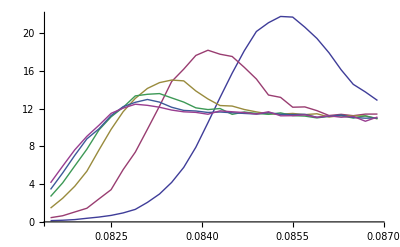

```mathematica
ListLinePlot[{dgdd[v][5],dgdd[v][10],dgdd[v][20],dgdd[v][30],dgdd[v][40],dgdd[v][50]}]
```

{{5000,21.7827},{10000,18.2019},{20000,15.0393},{30000,13.6051},{40000,12.9817},{50000,12.4773}}

{{Log[5000],3.08112},{Log[10000],2.90152},{Log[20000],2.71067},{Log[30000],2.61044},{Log[40000],2.56354},{Log[50000],2.52391}}

{{5000,0.0853},{10000,0.0841},{20000,0.0835},{30000,0.0833},{40000,0.0831},{50000,0.0829}}

{{5000,{}⟦1⟧},{10000,0.0207489},{20000,0.0196436},{30000,0.018822},{40000,0.0167011},{50000,0.0150547}}

{{5000,0.0275185},{10000,0.0207489},{20000,0.0196436},{30000,0.018822},{40000,0.0167011},{50000,0.0150547}}

{{Log[5000],-3.5929},{Log[10000],-3.87526},{Log[20000],-3.93},{Log[30000],-3.97273},{Log[40000],-4.09228},{Log[50000],-4.19607}}

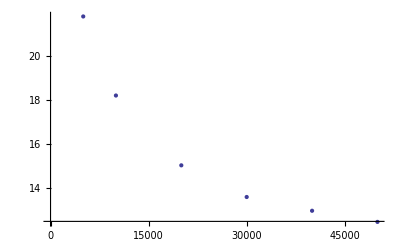

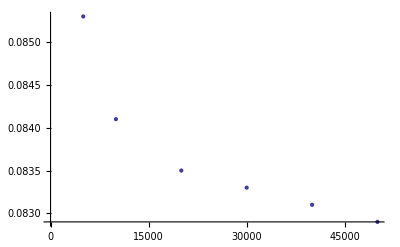

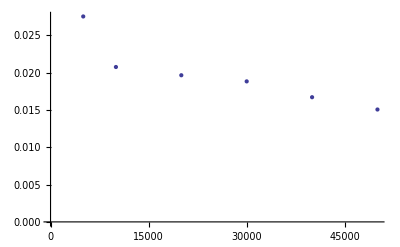

a0-b0 x

0.0812201+c0 x^-ex

{5.17122-0.246581 x, | Estimate | Standard Error | t-Statistic | P-Value
a0 | 5.17122 | 0.089136 | 58.015 | 5.28604×10^-7
b0 | 0.246581 | 0.00898058 | 27.4571 | 0.0000104641}

{-1.70367-0.226382 x, | Estimate | Standard Error | t-Statistic | P-Value
a0 | -1.70367 | 0.312288 | -5.45545 | 0.00548669
b0 | 0.226382 | 0.0314635 | 7.19506 | 0.00197724}

{0.0812201+0.101336/x^0.380103, | Estimate | Standard Error | t-Statistic | P-Value
ex | 0.380103 | 0.0227172 | 16.7319 | 0.0000747642
c0 | 0.101336 | 0.0216388 | 4.68307 | 0.00942614}

```mathematica
maxdgdd[v]=Table[{l*1000,Max[dgdd[v][l][[All,2]]]},{l,{5,10,20,30,40,50}}]
Logmaxdgdd[v]=Table[{Log[maxdgdd[v][[All,1]][[i]]],Log[maxdgdd[v][[All,2]][[i]]]},{i,1,Length[maxdgdd[v]]}]

pmaxdgdd[v]=Table[{maxdgdd[v][[All,1]][[i]],Select[dgdd[v][maxdgdd[v][[All,1]][[i]]/1000],#[[2]]==maxdgdd[v][[All,2]][[i]]&][[All,1]][[1]]},{i,1,Length[maxdgdd[v]]}]


vvpmaxdgdd[v]=Table[{pmaxdgdd[v][[All,1]][[i]],Select[gap[v][pmaxdgdd[v][[All,1]][[i]]/1000],#[[1]]==pmaxdgdd[v][[All,2]][[i]]&][[All,2]][[1]]},{i,1,Length[pmaxdgdd[v]]}]
vvpmaxdgdd[v]={{5000,0.027518491874999995},{10000,0.020748870000000003},{20000,0.01964359},{30000,0.01882197},{40000,0.01670109},{50000,0.015054660000000001}}


Logvvpmaxdgdd[v]=Table[{Log[vvpmaxdgdd[v][[All,1]][[i]]],Log[vvpmaxdgdd[v][[All,2]][[i]]]},{i,1,Length[vvpmaxdgdd[v]]}]


ListPlot[maxdgdd[v]]
ListPlot[pmaxdgdd[v]]
ListPlot[vvpmaxdgdd[v]]

ClearAll[a0,b0,d0,ex,c0]
model=a0-x*b0
model2=0.08122007942715888+c0*x^(-ex)

nlf1=NonlinearModelFit[Logmaxdgdd[v],model,{a0,b0},x];

nlf1[{"BestFit","ParameterTable"}]


nlf3=NonlinearModelFit[Logvvpmaxdgdd[v],model,{a0,b0},x];

nlf3[{"BestFit","ParameterTable"}]

nlf2=NonlinearModelFit[pmaxdgdd[v],model2,{ex,c0},x];

nlf2[{"BestFit","ParameterTable"}]
```

```mathematica
a[v]=0.22638171579816446
d0[v]=0.08122007942715888;
b0[v]=0.10133613937361555;
ex[v]=-0.3801025694705213;
```

0.226382

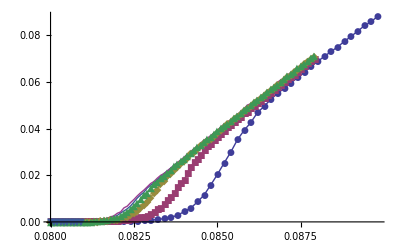

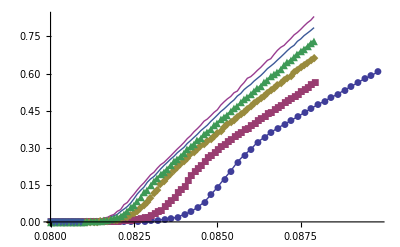

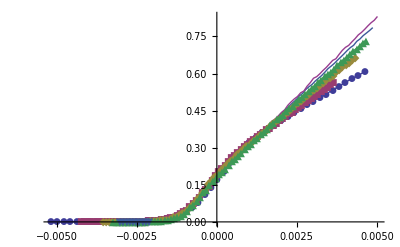

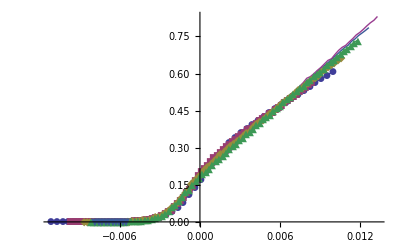

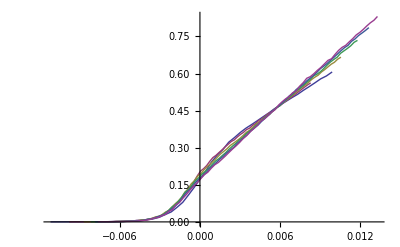

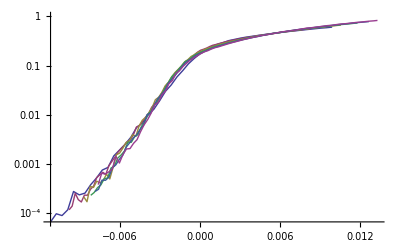

```mathematica
ClearAll[z]
z[v]=0.09;
Do[
gaps1[v][l]=Table[{gap[v][l][[All,1]][[i]],gap[v][l][[All,2]][[i]]*(1000*l)^a[v]},{i,1,Length[gap[v][l]]}];

gaps2[v][l]=Table[{gap[v][l][[All,1]][[i]]-(d0[v]+b0[v]*(l*1000)^(ex[v])),gap[v][l][[All,2]][[i]]*(1000*l)^a[v]},{i,1,Length[gap[v][l]]}];

gaps[v][l]=Table[{(gap[v][l][[All,1]][[i]]-(d0[v]+b0[v]*(l*1000)^(ex[v])))*(1000*l)^z[v],gap[v][l][[All,2]][[i]]*(1000*l)^a[v]},{i,1,Length[gap[v][l]]}];
,{l,{5,10,20,30,40,50}}]
pic0=ListPlot[{gap[v][5],gap[v][10],gap[v][20],gap[v][30],gap[v][40],gap[v][50]},Joined->True,PlotMarkers->Automatic,PlotRange->Full]
pic1=ListPlot[{gaps1[v][5],gaps1[v][10],gaps1[v][20],gaps1[v][30],gaps1[v][40],gaps1[v][50]},Joined->True,PlotMarkers->Automatic]
pic2=ListPlot[{gaps2[v][5],gaps2[v][10],gaps2[v][20],gaps2[v][30],gaps2[v][40],gaps2[v][50]},Joined->True,PlotMarkers->Automatic]
pic3=ListPlot[{gaps[v][5],gaps[v][10],gaps[v][20],gaps[v][30],gaps[v][40],gaps[v][50]},Joined->True,PlotMarkers->Automatic]
ListLinePlot[{gaps[v][5],gaps[v][10],gaps[v][20],gaps[v][30],gaps[v][40],gaps[v][50]}]
ListLogPlot[{gaps[v][5],gaps[v][10],gaps[v][20],gaps[v][30],gaps[v][40],gaps[v][50]},Joined->True]
```